```mathematica
$Assumptions={_∈Reals, h > 0, Vt > 0, d  > 0, A > 0};
	
TProduct[M__]:=KroneckerProduct[M]
σI = PauliMatrix[0];
σX = PauliMatrix[1];
σY = PauliMatrix[2];
σZ = PauliMatrix[3];
X = σX;
Y = σY;
Z = σZ;
σII = TProduct[σI, σI];
σIX = TProduct[σI, σX];
σIY = TProduct[σI, σY];
σIZ = TProduct[σI, σZ];
σXI = TProduct[σX, σI];
σXX = TProduct[σX, σX];
σXY = TProduct[σX, σY];
σXZ = TProduct[σX, σZ];
σYI = TProduct[σY, σI];
σYX = TProduct[σY, σX];
σYY = TProduct[σY, σY];
σYZ = TProduct[σY, σZ];
σZI = TProduct[σZ, σI];
σZX = TProduct[σZ, σX];
σZY = TProduct[σZ, σY];
σZZ = TProduct[σZ, σZ];

printAsPauliMatrices[M_] := (
σs = {σI, σX, σY, σZ};
letters = {"I", "X", "Y", "Z"};
output = {};
If[Length[M] == 2,(
Do[
term =  Total[Total[Conjugate[σs[[i]]]*M]]/Length[M];
If[!PossibleZeroQ[term],
output = Join[output, {ToString[term // FullSimplify, StandardForm], " σ", letters[[i]], " + "}];
];
,{i, 4}]
)];
If[Length[M] == 4, (
Do[
Do[
term =  Total[Total[Conjugate[TProduct[σs[[i]], σs[[j]]]]*M]]/Length[M] // FullSimplify;
If[!PossibleZeroQ[term],
output = Join[output, {ToString[term, StandardForm], " σ", letters[[i]], letters[[j]],  " + "}];
];
,{i, 4}];
,{j, 4}];
)];

Print[StringJoin[output[[;;Length[output] - 1]]]];
)

printWithBasis[M_,states_]:=(ML=Length[M];
newM=Table[If[(i==0&&j≠0),states[[j]],If[j==0&&i≠0,states[[i]],If[i==0&&j==0,"",M[[i]][[j]]]]],{i,0,ML},{j,0,ML}];
Print[MatrixForm[newM]])

stateString[state_, basis_, cutoff_:0] := (
output = {};
Do[
term = state[[i]];
If[Abs[term] > cutoff,
output = Join[output, {ToString[term], basis[[i]], " + "}]
];
,{i, Length[state]}];
StringJoin[output[[;;Length[output] - 1]]]
)


basisID = {"|i↓⇓>", "|i↓⇑>", "|i↑⇓>", "|i↑⇑>", "|d↓⇓>", "|d↓⇑>", "|d↑⇓>", "|d↑⇑>"};
basisGE = {"|g↓⇓>", "|g↓⇑>", "|g↑⇓>", "|g↑⇑>", "|e↓⇓>", "|e↓⇑>", "|e↑⇓>", "|e↑⇑>"};
basisGERotated = {"|g↓⇓>", "|g↓⇑>", "|g↑⇓> + |e↓⇑>", "|g↑⇑>", "|e↓⇓>", "|g↑⇓> - |e↓⇑>", "|e↑⇓>", "|e↑⇑>"};

Sx=(hBar/2)σX;
Sy=(hBar/2)σY;
Sz=(hBar/2)σZ;

Ix=(hBar/2)σX;
Iy=(hBar/2)σY;
Iz=(hBar/2)σZ;

SdotI=TProduct[Sx,Ix]+TProduct[Sy,Iy]+TProduct[Sz,Iz];

hBar=1;

transform[M_,U_]:=U.M.ConjugateTranspose[U]-ⅈ*hBar*U.ConjugateTranspose[D[U, t]]

(* SI units *)
setVariables[]:=(
B0=.2; (* T *)
d=15*10^-9; (* m *)
A=117*10^6; (* Hz *)
γe=27.97*10^9; (* Hz/T *)
γn=17.23*10^6; (* Hz/T *)
Δγ=-.002;
h=6.62607004*10^-34; (* J*s *)
e=-1.60217662*10^-19; (* C *)
Vt = γe*B0 + A/4; (* Hz *)
δB = γe*B0 - νB;
)

ϵ0 = √(Vt^2+(d^2 e^2 ΔE^2)/h^2);

clearVariables[]:=Clear[B0,Bac,νB,γe,γn,Δγ,A,Aac,ΔE,Eac,νE,Vt,d,h, e, δB, δE, δ]
clearVariables[]
```

```mathematica
HorbBase = Vt/2 σX-((e*ΔE*d)/(2h))σZ
{β, α} = Eigensystem[HorbBase][[2]][[2]] // Normalize // FullSimplify
α = -α;

iState = {α, β};
dState = {β, -α};
ii = Outer[Times, iState, iState] // FullSimplify;
id = Outer[Times, iState, dState] // FullSimplify;
di = Outer[Times, dState, iState] // FullSimplify;
dd = Outer[Times, dState, dState] // FullSimplify;

(* HB0 negative to make the order of spins down-up, not up-down *)
HB0=-B0 (γe*TProduct[(σI+Δγ*dd),Sz, σI]-γn*TProduct[σI,σI, Iz]);
HA=TProduct[A*dd,SdotI];
Horb=TProduct[-((e*(ΔE + Eac)*d)/(2h))*(ii - dd) + (Vt/2)(id + di), σI, σI];
HESR = Bac(γe*TProduct[σI,Sx, σI]-γn*TProduct[σI,σI, Ix]);

H = HB0 + HESR + HA + Horb;

energiesAt[Ef_, M_] := Eigensystem[M /. {ΔE -> Ef}][[1]]
energiesInOrder[Ef_, M_] := energiesAt[Ef, M][[order[Ef, M]]]
statesAt[Ef_, M_] := Eigensystem[M /. {ΔE -> Ef}][[2]]
statesInOrder[Ef_, M_] := statesAt[Ef, M][[order[Ef, M]]]

targetStates = IdentityMatrix[8];
order[Ef_, M_] := Table[Ordering[row, -1][[1]], {row,Abs[targetStates.ConjugateTranspose[statesAt[Ef, M]]]}]
putInOrder[Q_, Ef_, M_] := Q[[order[Ef, M]]]

window[t_?NumericQ, τ_, T_] := Piecewise[{{(1 - Cos[π*t/τ])/2, 0 < t < τ}, {(1 - Cos[π*(T - t)/τ])/2, (T - τ) < t < T}, {1, τ ≤ t ≤ T - τ}}, 0]
tanhWindow[t_?NumericQ, τ_, T_] := Piecewise[{{(Tanh[t/(4τ)] - Tanh[0/(4τ)] - Tanh[(t - T)/(4τ)] + Tanh[-T/(4τ)]), 0 < t < T}}, 0]

Λ = IdentityMatrix[8];
Λ[[3]][[3]] = 1/Sqrt[2];
Λ[[3]][[6]] = 1/Sqrt[2];
Λ[[6]][[3]] = 1/Sqrt[2];
Λ[[6]][[6]] = -1/Sqrt[2];
```

{{-(d e ΔE)/(2 h),Vt/2},{Vt/2,(d e ΔE)/(2 h)}}

{(√(1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))))/(√2),1/(√(1+((-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))^2)/(h^2 Vt^2)))}

```mathematica
(* PLOT EVOLUTION UNDER DRIVING FIELDS *)
```

0.963139

9.8×10^-8

{0.00102046,0.950466,0.00205971,0.00379911,0.000436556,0.0414584,0.00071931,0.000168582}

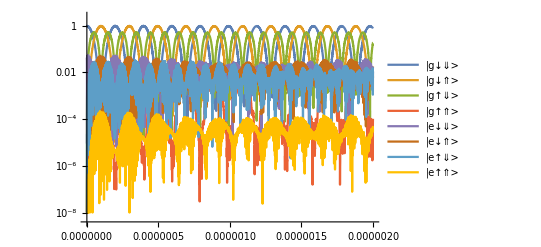

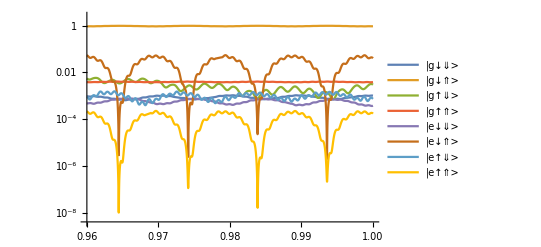

```mathematica
Tmax = 1000*10^-9;

Clear[findEvolution];
findEvolution[ΔEin_?NumericQ, B0in_?NumericQ, Eacin_, Bacin_, δEin_?NumericQ, δBin_?NumericQ] := (
setVariables[];
Clear[Eff, EeSpin, EnSpin, undrivenStates, ψ0, funcs, equations, state];

ΔE = ΔEin;
B0 = B0in;

Bac = 0;
Eac = 0;

Eff = (energiesInOrder[0, H][[3]] - energiesInOrder[0, H][[2]]);
EeSpin = (energiesInOrder[0, H][[3]] - energiesInOrder[0, H][[1]]);
undrivenStates = statesInOrder[0, H];

Bac = Bacin;
Eac = Eacin;
νB = (EeSpin - δBin);
νE = (Eff - δEin);

M = 2*π*H;

ψ0 = undrivenStates[[1]];

funcs=Array[ψ[#1][t]&,{Length[ψ0]}];

equations=Flatten@Join[Thread[M.funcs == ⅈ*D[funcs,t]],Thread[funcs==ψ0/.t->0]];

state= NDSolveValue[equations,funcs,{t,-Tmax/100,101*Tmax/100}];

clearVariables[];
Clear[Eff, EeSpin, EnSpin, undrivenStates, ψ0, funcs, equations];

state
)

averageBits = (Tmax/1000)*RandomReal[{-5, 5}, 100];

bestSoFar = 0;
bestT = 0;
bestParameters = {};

Clear[maxGDUcoefficient];
maxGDUcoefficient[ΔEin_?NumericQ, B0in_?NumericQ, Eacin_, Bacin_, δE_?NumericQ, δB_?NumericQ] := (
state = findEvolution[ΔEin, B0in, Eacin, Bacin, δE, δB];
state = Abs[state]^2;

ts = Table[t, {t, 0, Tmax, Tmax/1000}];
otherSum = state[[1]] + state[[3]] + state[[4]] + state[[5]] + state[[6]] + state[[7]] + state[[8]];
samples = Table[1 - Sum[(otherSum) /.{t->(tt + dt)}, {dt, averageBits}]/Length[averageBits], {tt, 0, Tmax, Tmax/1000}];
maxSample = Max[samples];

If[maxSample > bestSoFar, (bestSoFar = maxSample; bestParameters = {ΔEin, B0in, Eacin, Bacin, δE, δB}; bestT = N[ts[[Ordering[samples, -1]]][[1]]]; (*Print[{bestSoFar, bestParameters}]*))];

maxSample
)
GDUcoefficientAtEnd[ΔEin_?NumericQ, B0in_?NumericQ, Eacin_, Bacin_, δE_?NumericQ, δB_?NumericQ] := (
state = findEvolution[ΔEin, B0in, Eacin, Bacin, δE, δB];
state = Abs[state]^2;

otherSum = state[[1]] + state[[3]] + state[[4]] + state[[5]] + state[[6]] + state[[7]] + state[[8]];
endCoefficient = 1 - Sum[(otherSum) /.{t->(Tmax + dt)}, {dt, averageBits}]/Length[averageBits];

If[endCoefficient > bestSoFar, (bestSoFar = endCoefficient; bestParameters = {ΔEin, B0in, Eacin, Bacin, δE, δB}; bestT = Tmax; (*Print[{bestSoFar, bestParameters}]*))];

maxSample
)

bestSoFar = 0;
bestT = 0;
bestParameters = {};

Tmax = Tmax*2;
(*maxGDUcoefficient[0, .8*.2*1.0056, 200, .0007, 2*10^7, 2*10^7]*)
maxGDUcoefficient[-68.63253962234526,0.1654317731042863,124.9636646*Cos[2*π*νE*t],0.00051832529*Cos[2*π*νB*t],-171728.42293817864,-171728.42293817864]
bestT
state /. {t->bestT}
LogPlot[Evaluate@Table[Max[state[[i]], 10^-8], {i, Length[state]}],{t,0,Tmax}, PlotRange->All, PlotLegends->basisGE]
LogPlot[Evaluate@Table[Max[state[[i]], 10^-8], {i, Length[state]}],{t,bestT - Tmax/1000, bestT + Tmax/1000}, PlotRange->All, PlotLegends->basisGE]
Tmax = Tmax/2;
```